## Constants, Units and Parameters

```mathematica
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"];
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;THz=10^12;
m=1;cm=10^-2;mm=10^-3;μm=10^-6;nm=10^-9;pm=10^-12;
s=1;ms=10^-3;μs=10^-6;ns=10^-9;ps=10^-12;
Gauss=10^-4;mG=10^-3 Gauss;μG=10^-6 Gauss;T=1;
mW=10^-3;μW=10^-6;
c=2.99792458 10^8 m/s;
μ0=4π 10^-7;
ϵ0=1/(μ0 c^2);
h=6.62606896 10^-34;
ℏ=h/(2π);
e=1.602176487 10^-19;
μB=9.27400915 10^-24;
AMU=1.660538782 10^-27;
AME=9.10938215 10^-31;
a0=0.52917720859 10^-10 m;
kB=1.3806504 10^-23;
Kelvin=1;μK=10^-6 Kelvin;nK=10^-9 Kelvin;

AbundanceK39=93.2581 0.01;
AbundanceK40=0.0117 0.01;
AbundanceK41=6.7302 0.01;
massK39=38.96370668AMU;
massK40=39.96399848AMU;
massK41=40.96182576 AMU;
Meltingpoint=336.8K;
Boilingpoint=1047.15K;

λD1K40=770.108136507nm;
ΓD1K40=2π 5.956MHz;
ωD1K40=c/λD1K40 2π;
λD2K40=766.700674872nm;
ΓD2K40=2π 6.035MHz;
ωD2K40=c/λD2K40 2π;

AhfGroundK40=-285.7308MHz;
AhfD1K40=-34.523MHz;
AhfD2K40=-7.585MHz;
BhfD2K40=-3.445MHz;
gs=2.0023193043622;
gIK40=0.000176490;
gJGround=2.00229421;
gJD1=2./3;
gJD2=4./3;

λtrap=1053.57nm;
ωtrap=c/λtrap 2π;
λlat=λtrap;
ωlat=ωtrap;
klat=(2π)/λlat;
Erecoil=(ℏ^2 klat^2)/(2 massK40);
```

## lattice parameters

```mathematica
(*Lattice parameters*)
```

```mathematica
Vlatx=2.5;(*unit: Er*)
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;

(*angles*)
(*-Graphics-*)
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
Clear[hh,kk];
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧
xdt1toylat=solangle⟦1,2,2⟧
```

{{hh→-0.432367,kk→0.89142}}

-0.432367

0.89142

### do not project along one lattice direction. Assumption : isotropic cubic lattice

```mathematica
xdt1toxlat=1;
xdt1toylat=0;
```

## overall trap frequency (including harmonic confinement of lattice beams)

```mathematica
λlat=1054nm;
klat=(2π)/λlat;
Er=(ℏ^2 klat^2)/(2 massK40);
w0x=60μm;
w0y=60μm;
w0z=85μm;

xdt1=0.5;
xdtfreq=√(xdt1*1000)*3.29116-15.03525
xdtfreq=32;


fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π)
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
f0= √(1*xdtfreq^2+fx^2)
```

58.5573

56.8725

56.8725

65.7086

65.257

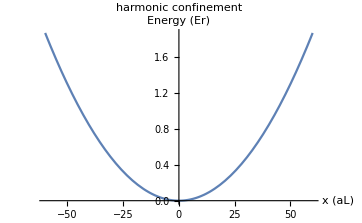

```mathematica
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Plot[potential[x,f0],{x,-60,60},PlotLabel->"harmonic confinement",AxesLabel->{"x (aL)","Energy (Er)"}]
```

```mathematica
onsiteU=0.407634 h kHz/Erecoil (174(1-7.5/(206-202.1)))/174 
tunnelling= 0.12642;(*unit is Erecoil*)
tempβ=4;
(*1/(kB Temp) = 1/Er*)
```

-0.0836618

## density fitting

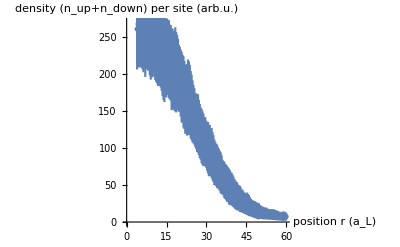

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

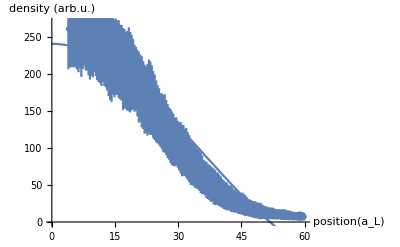

{{1.01833,-2.25864,2000.,-94.5464,652.24,0.218441,337.441,6.50452}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -2.25864 | 0.218441 | -10.3399 | 1.46251×10^-19
ampx | 2000. | 337.441 | 5.92697 | 1.80107×10^-8
offsetx | -94.5464 | 6.50452 | -14.5355 | 3.5806×10^-31

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

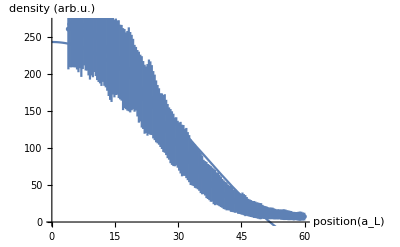

{{1.0627,-2.18359,2000.,-87.8898,618.582,0.216314,357.228,5.85133}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -2.18359 | 0.216314 | -10.0945 | 6.81185×10^-19
ampx | 2000. | 357.228 | 5.59866 | 9.04863×10^-8
offsetx | -87.8898 | 5.85133 | -15.0205 | 1.66891×10^-32

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

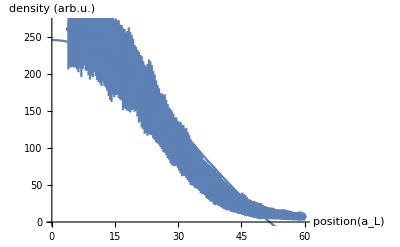

{{1.11111,-2.10345,2000.,-81.6813,596.178,0.309192,546.632,6.35628}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -2.10345 | 0.309192 | -6.80305 | 1.8807×10^-10
ampx | 2000. | 546.632 | 3.65877 | 0.000342413
offsetx | -81.6813 | 6.35628 | -12.8505 | 1.66045×10^-26

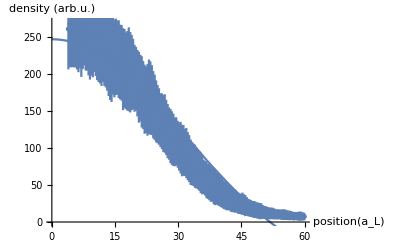

{{1.16414,-2.02965,2000.,-74.0773,538.098,0.241376,446.096,5.39245}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -2.02965 | 0.241376 | -8.4087 | 2.03505×10^-14
ampx | 2000. | 446.096 | 4.48334 | 0.0000138481
offsetx | -74.0773 | 5.39245 | -13.7372 | 5.73652×10^-29

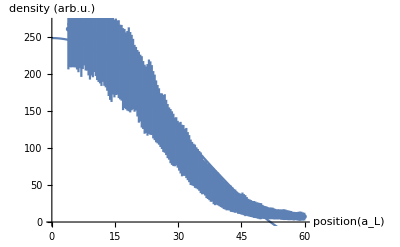

{{1.22249,-1.95423,2000.,-66.7831,485.555,0.149423,289.503,4.16278}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.95423 | 0.149423 | -13.0785 | 3.85897×10^-27
ampx | 2000. | 289.503 | 6.90839 | 1.06242×10^-10
offsetx | -66.7831 | 4.16278 | -16.0429 | 2.75957×10^-35

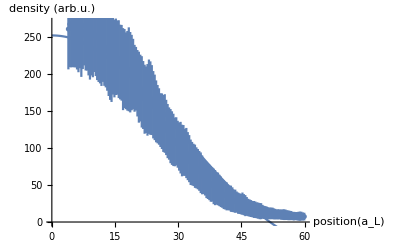

{{1.287,-1.8669,2000.,-61.2487,466.477,0.13222,282.545,3.36814}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.8669 | 0.13222 | -14.1196 | 5.02049×10^-30
ampx | 2000. | 282.545 | 7.07853 | 4.18472×10^-11
offsetx | -61.2487 | 3.36814 | -18.1847 | 5.68197×10^-41

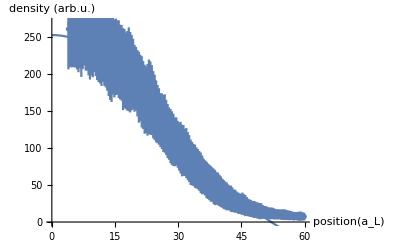

{{1.3587,-1.79359,2000.,-52.7915,381.917,0.140391,306.158,3.51537}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.79359 | 0.140391 | -12.7757 | 2.68034×10^-26
ampx | 2000. | 306.158 | 6.53257 | 7.97952×10^-10
offsetx | -52.7915 | 3.51537 | -15.0173 | 1.70223×10^-32

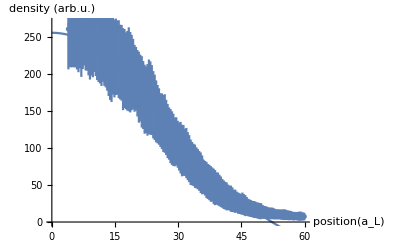

{{1.43885,-1.71062,2000.,-45.9107,329.74,0.172085,404.676,3.43807}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.71062 | 0.172085 | -9.94058 | 1.78155×10^-18
ampx | 2000. | 404.676 | 4.94222 | 1.91219×10^-6
offsetx | -45.9107 | 3.43807 | -13.3536 | 6.64353×10^-28

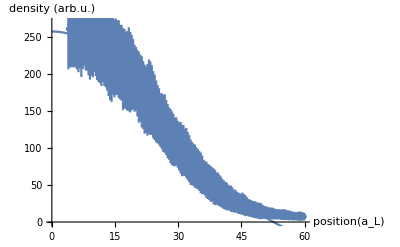

{{1.52905,-1.62709,2000.,-38.5506,261.833,0.0839634,208.427,2.42016}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.62709 | 0.0839634 | -19.3786 | 4.80065×10^-44
ampx | 2000. | 208.427 | 9.59567 | 1.51673×10^-17
offsetx | -38.5506 | 2.42016 | -15.9289 | 5.61051×10^-35

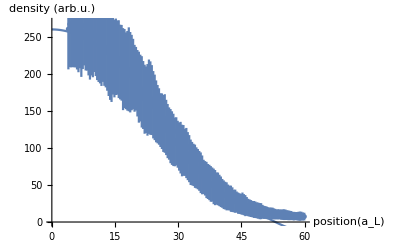

{{1.63132,-1.54013,2000.,-31.6725,203.989,0.0742911,195.084,2.10737}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.54013 | 0.0742911 | -20.7311 | 1.95353×10^-47
ampx | 2000. | 195.084 | 10.252 | 2.53967×10^-19
offsetx | -31.6725 | 2.10737 | -15.0294 | 1.57777×10^-32

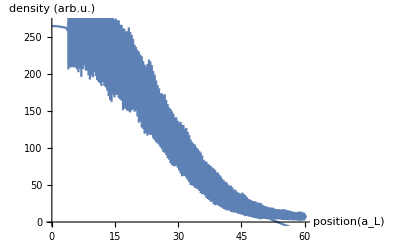

{{1.74825,-1.44908,1999.99,-25.4172,155.674,0.103818,302.433,1.93314}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.44908 | 0.103818 | -13.9579 | 1.40548×10^-29
ampx | 1999.99 | 302.433 | 6.61301 | 5.20869×10^-10
offsetx | -25.4172 | 1.93314 | -13.1482 | 2.47141×10^-27

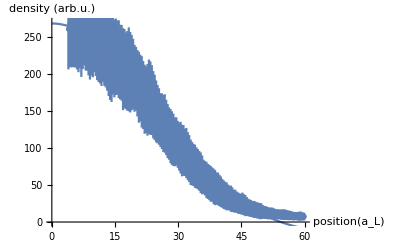

{{1.88324,-1.35839,2000.,-19.0407,107.382,0.0544832,171.568,1.29677}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.35839 | 0.0544832 | -24.9323 | 2.47913×10^-57
ampx | 2000. | 171.568 | 11.6572 | 3.436×10^-23
offsetx | -19.0407 | 1.29677 | -14.6832 | 1.40479×10^-31

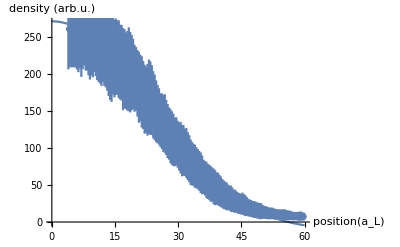

{{2.04082,-1.27016,2000.,-11.9934,57.1601,0.0379696,126.558,1.00723}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.27016 | 0.0379696 | -33.452 | 1.21287×10^-74
ampx | 2000. | 126.558 | 15.8031 | 1.23004×10^-34
offsetx | -11.9934 | 1.00723 | -11.9074 | 6.94762×10^-24

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {5.86338×10^-10,0.0000950457,2.93169×10^-10}, is returned.

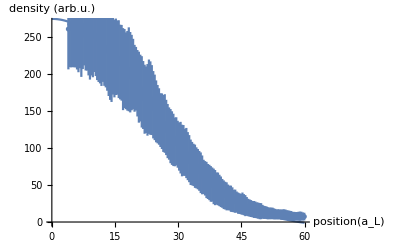

{{2.22717,-1.09629,1722.29,-6.47328,28.7773,0.0303816,93.6166,0.803469}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -1.09629 | 0.0303816 | -36.0839 | 2.41179×10^-79
ampx | 1722.29 | 93.6166 | 18.3973 | 1.5919×10^-41
offsetx | -6.47328 | 0.803469 | -8.05667 | 1.61614×10^-13

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {6.47968×10^-8,0.00618151,3.23984×10^-8}, is returned.

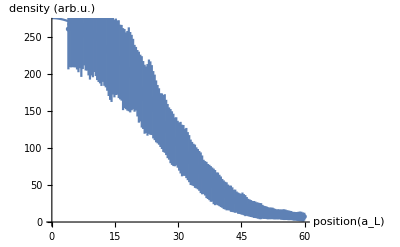

{{2.45098,-0.892027,1375.13,-2.02053,13.0806,0.0166508,41.6871,0.633061}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.892027 | 0.0166508 | -53.5727 | 5.73547×10^-105
ampx | 1375.13 | 41.6871 | 32.9868 | 8.78094×10^-74
offsetx | -2.02053 | 0.633061 | -3.19169 | 0.00169912

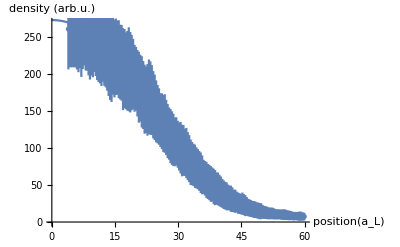

{{2.7248,-0.65522,1007.85,1.00187,6.33482,0.00974526,17.0339,0.529535}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.65522 | 0.00974526 | -67.2348 | 2.92374×10^-120
ampx | 1007.85 | 17.0339 | 59.1674 | 1.28292×10^-111
offsetx | 1.00187 | 0.529535 | 1.89198 | 0.0602776

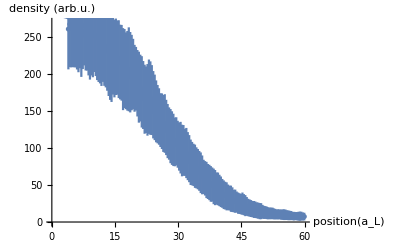

{{3.06748,-0.591606,1000.,7.25096,2.66402,0.0109689,21.1745,0.645009}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.591606 | 0.0109689 | -53.9349 | 2.03956×10^-105
ampx | 1000. | 21.1745 | 47.2267 | 1.25101×10^-96
offsetx | 7.25096 | 0.645009 | 11.2416 | 4.8588×10^-22

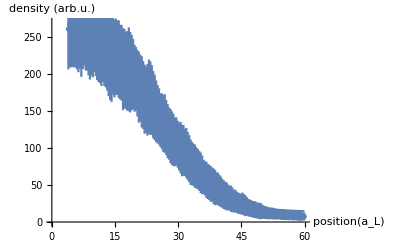

{{3.50877,-0.534866,1000.,13.9441,33.8812,0.0184237,40.207,1.05451}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.534866 | 0.0184237 | -29.0314 | 4.32174×10^-66
ampx | 1000. | 40.207 | 24.8713 | 3.39812×10^-57
offsetx | 13.9441 | 1.05451 | 13.2233 | 1.52808×10^-27

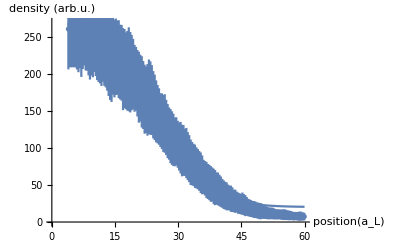

{{4.09836,-0.478776,1000.,20.3567,110.205,0.0241794,59.1257,1.55092}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.478776 | 0.0241794 | -19.801 | 4.09129×10^-45
ampx | 1000. | 59.1257 | 16.9131 | 1.27481×10^-37
offsetx | 20.3567 | 1.55092 | 13.1256 | 2.8555×10^-27

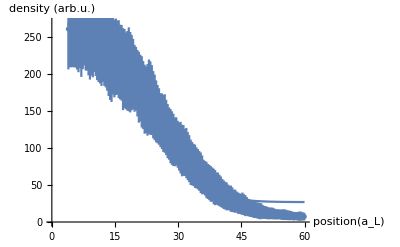

{{4.92611,-0.425811,1000.,26.9309,250.557,0.0279904,77.9422,2.07879}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.425811 | 0.0279904 | -15.2127 | 4.97349×10^-33
ampx | 1000. | 77.9422 | 12.83 | 1.89285×10^-26
offsetx | 26.9309 | 2.07879 | 12.9551 | 8.50096×10^-27

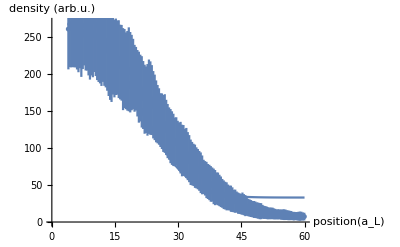

{{6.17284,-0.376671,1000.,33.091,447.711,0.0286673,91.2169,2.62137}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.376671 | 0.0286673 | -13.1394 | 2.61401×10^-27
ampx | 1000. | 91.2169 | 10.9629 | 2.85663×10^-21
offsetx | 33.091 | 2.62137 | 12.6236 | 7.09783×10^-26

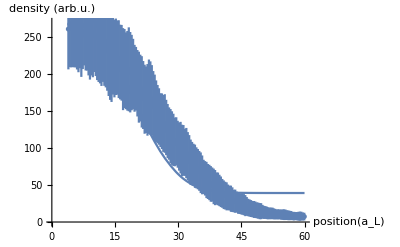

{{8.26446,-0.334173,1000.,39.2157,710.209,0.0327922,120.102,3.1652}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.334173 | 0.0327922 | -10.1906 | 3.73157×10^-19
ampx | 1000. | 120.102 | 8.32627 | 3.31591×10^-14
offsetx | 39.2157 | 3.1652 | 12.3896 | 3.17404×10^-25

```mathematica
(*data input*)
startid=12;

rawdatatemp=ToExpression[Import["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\data analysis\\2.5Er 3Aug 2017\\206G\\temp\\AT_temp_iXon_2.5Er_206G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin_50ms_wait\\temp.txt","TSV"]];

datainput1=Table[{rawdatatemp⟦ii,1⟧(0.18μm)/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}];
datainput=Select[datainput1,#⟦1⟧≤ 60&];
ErrorListPlot[datainput,AxesLabel->{"position r (a_L)","density (n_up+n_down) per site (arb.u.)"}]
(*MC data input*)
path=NotebookDirectory[];
path=StringJoin[path,"\\results.txt"];
resulttemp=ToExpression[Import[path,"TSV"]];
result=resulttemp;
tempβlist=Union[result⟦All,1⟧];
tempβnum=Length[tempβlist];

(*fitting*)

fitls={{0}};

For[iitempβ=1,iitempβ≤tempβnum,iitempβ++,
{
tempβcheck=tempβlist⟦iitempβ⟧;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*√(densityerrcheckfunc[μfitxx-potential[positionxx,f0]]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0]]^2);

sol=NonlinearModelFit[datainput⟦All,{1,2}⟧,{finalρfunc[xx,μx,ampx,offsetx],1000≤ ampx≤ 2000},{{μx,-1},{ampx,1500},{offsetx,0}},{xx}];
sol1=sol["ParameterTable"];
μfit=sol1⟦1,1,2,2⟧;
ampfit=sol1⟦1,1,3,2⟧;
offsetfit=sol1⟦1,1,4,2⟧;
μfiterr=sol1⟦1,1,2,3⟧;
ampfiterr=sol1⟦1,1,3,3⟧;
offsetfiterr=sol1⟦1,1,4,3⟧;

(*
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/ampfit^2/(1+0 finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
*)
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/1/(datainput⟦ii,3⟧^2+finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
χsquare=Total[χlist];

Print[Show[ErrorListPlot[datainput,AxesLabel->{"position(a_L)","density (arb.u.)"}],Plot[finalρfunc[x,μfit,ampfit,offsetfit],{x,0,60}]]];
fitlstemp={{tempβcheck,μfit,ampfit,offsetfit,χsquare,μfiterr,ampfiterr,offsetfiterr}};
Print[fitlstemp];
Print[sol1];
If[ampfit≥ 2500,
{
Print["bad fitting"];
},
fitls=Join[fitls,fitlstemp]
];


}
]
fitls=fitls⟦2;;Length[fitls]⟧;
```

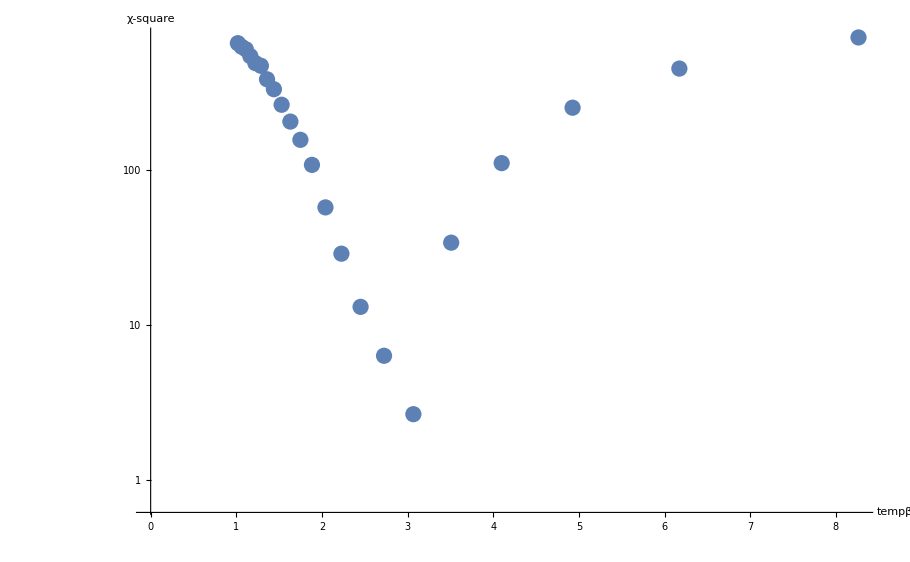

{tempβ,μ,amp,offset,χ-square,μerr,amperr,offseterr}

{3.06748,-0.591606,1000.,7.25096,2.66402,0.0109689,21.1745,0.645009}

3.06748

-0.591606

1000.

7.25096

temp (Er): 0.326

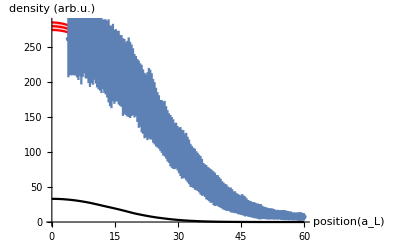

```mathematica
pchi=ListLogPlot[fitls⟦All,{1,5}⟧,AxesLabel->{"tempβ","χ-square"}]
Print[{"tempβ","μ","amp","offset","χ-square","μerr","amperr","offseterr"}]
res=Sort[fitls,#1⟦5⟧<#2⟦5⟧&]⟦1⟧
tempβfit=res⟦1⟧
μfit=res⟦2⟧
ampfit=res⟦3⟧
offsetfit=res⟦4⟧

Print[StringJoin["temp (Er): ",ToString[1/tempβfit]]]

tempβcheck=tempβfit;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5;

p1=Show[
Plot[{finalρfunc[x,μfit,ampfit,offsetfit],
finalρfunc[x,μfit,ampfit,offsetfit]-finalρerrfunc[x,μfit,ampfit],
finalρfunc[x,μfit,ampfit,offsetfit]+finalρerrfunc[x,μfit,ampfit]
}
,{x,0,60},PlotStyle->{Red},AxesLabel->{"position(a_L)","density (arb.u.)"},Filling->{2->{3}}]
,ErrorListPlot[datainput],
Plot[finaldoublonfunc[x,μfit,ampfit],{x,0,60},PlotStyle->{Black}]

]
```

2.84331

3.09755

tempβerr =

0.127122

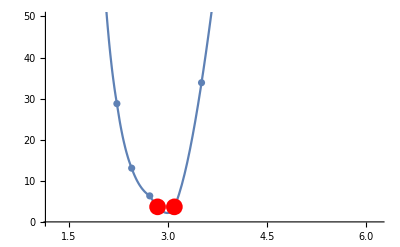

```mathematica
ampfit=res⟦3⟧;

lengdata=Length[datainput];
newchi2=Table[{fitls⟦All,{1,5}⟧⟦ii,1⟧,(fitls⟦All,{1,5}⟧⟦ii,2⟧)/(1+0lengdata)},{ii,1,Length[fitls]}];
newchifitlist=Select[newchi2,#⟦2⟧≤ 500&];
newres=Sort[newchi2,#1⟦2⟧<#2⟦2⟧&]⟦1⟧;
tempβminnew=newres⟦1⟧;
newchifitfunc=Interpolation[newchifitlist];
ffuncg[x_]:=newchifitfunc[X]/.X-> x;
desirechi=Min[newchifitlist⟦All,2⟧]+1;
tempβerrpoint1=FindRoot[ffuncg[x]==desirechi,{x,tempβminnew-0.2}]⟦1,2⟧
tempβerrpoint2=FindRoot[ffuncg[x]==desirechi,{x,tempβminnew+0.2}]⟦1,2⟧
Print["tempβerr = "];
Abs[(tempβerrpoint1-tempβerrpoint2)/2]

Show[ListPlot[newchifitlist,PlotRange->{0,50}],
Plot[ffuncg[x],{x,tempβminnew-1,tempβminnew+1}],ListPlot[{{tempβerrpoint1,desirechi},{tempβerrpoint2,desirechi}},PlotStyle->{PointSize[0.03],Red}]]
```

```mathematica
Export["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\Monte Carlo\\quest-1.4.4\\test1\\2.5Er 206G\\2.5Er 206G.emf",p1,"emf"]
Export["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\Monte Carlo\\quest-1.4.4\\test1\\2.5Er 206G\\2.5Er 206G pchi.emf",pchi,"emf"]
```

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\Monte Carlo\quest-1.4.4\test1\2.5Er 206G\2.5Er 206G.emf

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\Monte Carlo\quest-1.4.4\test1\2.5Er 206G\2.5Er 206G pchi.emf

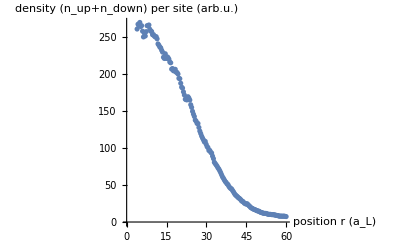

{2.45098,-0.892027,1375.13,-2.02053,0.00119501,0.0166508,41.6871,0.633061}

2.45098

-0.892027

1375.13

-2.02053

temp (Er): 0.408

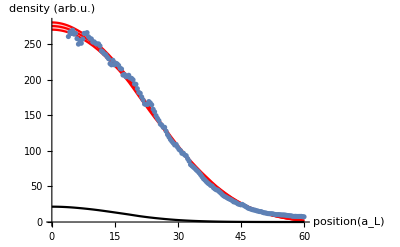

```mathematica
startid=12;

rawdatatemp=ToExpression[Import["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\data analysis\\2.5Er 3Aug 2017\\206G\\temp\\AT_temp_iXon_2.5Er_206G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin_50ms_wait\\temp.txt","TSV"]];

datainput1=Table[{rawdatatemp⟦ii,1⟧(0.18μm)/(λlat/2),rawdatatemp⟦ii,2⟧},{ii,startid,Length[rawdatatemp]}];
datainput=Select[datainput1,#⟦1⟧≤ 60&];
ListPlot[datainput,AxesLabel->{"position r (a_L)","density (n_up+n_down) per site (arb.u.)"}]
(*MC data input*)
path=NotebookDirectory[];
path=StringJoin[path,"\\results.txt"];
resulttemp=ToExpression[Import[path,"TSV"]];
result=resulttemp;
tempβlist=Union[result⟦All,1⟧];
tempβnum=Length[tempβlist];


res={2.450980392156863,-0.8920269224441666,1375.1253165574878,-2.020533916578205,0.001195010567193326,0.016650780999035927,41.687077353316475,0.6330609008499594};
tempβfit=res⟦1⟧
μfit=res⟦2⟧
ampfit=res⟦3⟧
offsetfit=res⟦4⟧

Print[StringJoin["temp (Er): ",ToString[1/tempβfit]]]

tempβcheck=tempβfit;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5;

p1=Show[
Plot[{finalρfunc[x,μfit,ampfit,offsetfit],
finalρfunc[x,μfit,ampfit,offsetfit]-finalρerrfunc[x,μfit,ampfit],
finalρfunc[x,μfit,ampfit,offsetfit]+finalρerrfunc[x,μfit,ampfit]
}
,{x,0,60},PlotStyle->{Red},AxesLabel->{"position(a_L)","density (arb.u.)"},Filling->{2->{3}}]
,ListPlot[datainput],
Plot[finaldoublonfunc[x,μfit,ampfit],{x,0,60},PlotStyle->{Black}]

]
```

## New demarco density err calculation

temp (Er): 0.326

{tempβfit,tempβfiterr,μfit,μfiterr}

{3.06748,0.441287,-0.591606,0.0109689}

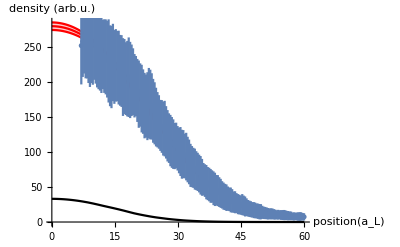

```mathematica
startid=7;
endid=60;

rawdatatemp=ToExpression[Import["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\data analysis\\2.5Er 3Aug 2017\\206G\\temp\\AT_temp_iXon_2.5Er_206G_XDT1_0.15_ramp_150ms_60Hz_amp_1pp_xlat_10k_0.1msPin_50ms_wait\\temp.txt","TSV"]];

datainput1=Table[{rawdatatemp⟦ii,1⟧(0.18μm)/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}];
datainput=Select[datainput1,(#⟦1⟧≤ endid&&#⟦1⟧≥ startid)&];
(*ListPlot[datainput,AxesLabel->{"position r (a_L)","density (n_up+n_down) per site (arb.u.)"}]*)
(*MC data input*)
path=NotebookDirectory[];
path=StringJoin[path,"\\results.txt"];
resulttemp=ToExpression[Import[path,"TSV"]];
result=resulttemp;
tempβlist=Union[result⟦All,1⟧];
tempβnum=Length[tempβlist];


res={3.067484662576687,-0.5916059418019215,1000.0000039525848,7.250957081474479,2.6640246734200006,0.010968897125284425,21.174451537097287,0.6450085201942946};

tempβfit=res⟦1⟧;
μfit=res⟦2⟧;
ampfit=res⟦3⟧;
offsetfit=res⟦4⟧;
μfiterr=res⟦6⟧;
Print[StringJoin["temp (Er): ",ToString[1/tempβfit]]];
tempβcheck=tempβfit;
tempβerrlisttemp=Sort[tempβlist,Abs[#1-tempβfit]≤ Abs[#2-tempβfit]&];
tempβfiterr=Max[Abs[tempβerrlisttemp⟦3⟧-tempβerrlisttemp⟦1⟧],Abs[tempβerrlisttemp⟦2⟧-tempβerrlisttemp⟦1⟧]];
Print[{"tempβfit","tempβfiterr","μfit","μfiterr"}];
Print[{tempβfit,tempβfiterr,μfit,μfiterr}];
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5;

p1=Show[
Plot[{finalρfunc[x,μfit,ampfit,offsetfit],
finalρfunc[x,μfit,ampfit,offsetfit]-finalρerrfunc[x,μfit,ampfit],
finalρfunc[x,μfit,ampfit,offsetfit]+finalρerrfunc[x,μfit,ampfit]
}
,{x,0,60},PlotStyle->{Red},AxesLabel->{"position(a_L)","density (arb.u.)"},Filling->{2->{3}}]
,ErrorListPlot[datainput],
Plot[finaldoublonfunc[x,μfit,ampfit],{x,0,60},PlotStyle->{Black}]

]

(*3D trap frequencies*)
f0horizontal=f0;
f0vertical=√(fz^2+(xdtfreq*200/30)^2);
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;
dx=1;
dy=1;
dz=1;
```

### density weighted density and err calculation

{0.136081,0.0076986}

{0.137591,0.00786515}

{0.139113,0.00803466}

{0.140648,0.00820718}

{0.142196,0.00838275}

{0.143757,0.00856149}

0.346884+0.349872 x

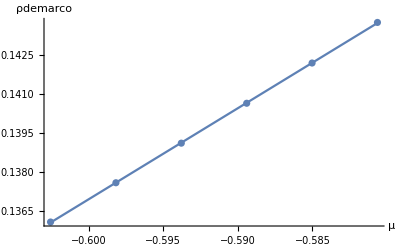

0.0313931+0.0393305 x

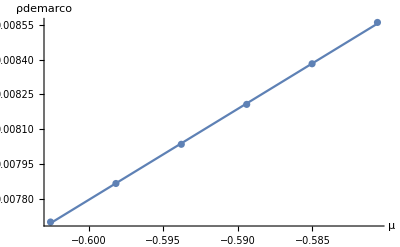

```mathematica
(*calculate μ related err slope*)
iiμlength=5;
μrelatederrslopelist={0};
For[iiμ=1,iiμ≤ iiμlength+1,iiμ++,
{
(*find corresponding μ and temp list*)
μchecktemp=(μfit-μfiterr)+(iiμ-1)*(2 μfiterr)/iiμlength;
tempβcheck=tempβfit;
(*find corresponding μ and temp list*)
(*data interpolation*)
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,3}⟧]];
densityerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,4}⟧]];
doubloncheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,5}⟧]];
doublonerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,6}⟧]];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=Quiet[ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx];
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5];
finaldoublonerrfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*doublonerrcheckfunc[μfitxx-potential[positionxx,f0]]];
(*data interpolation*)

(*calculated demarco density err*)
iixmax=40;
iiymax=40;
iizmax=20;
finalρfunc3d[iix_,iiy_,iiz_]:=Quiet[densitycheckfunc[μchecktemp-vext[iix,iiy,iiz]]];
finaldoublon3d[iix_,iiy_,iiz_]:=Quiet[doubloncheckfunc[μchecktemp-vext[iix,iiy,iiz]]];

final3dρlist=Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];
final3ddoublonlist=Table[{iix,iiy,iiz,Max[0,finaldoublon3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];

dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4⟧^2,{ii,1,Length[ls3dρ]}]];
doublondemarcon2=Total[Table[ls3dρ⟦ii,4⟧*ls3ddoublon⟦ii,4⟧,{ii,1,Length[ls3dρ]}]];
ntot=Total[ls3dρ⟦All,4⟧];
ρdemarco=ρdemarcon2/ntot;
doublondemarco=doublondemarcon2/ntot;
Print[{ρdemarco,doublondemarco}];
μrelatederrslopelisttemp={{μchecktemp,ρdemarco,doublondemarco}};
μrelatederrslopelist=Join[μrelatederrslopelist,μrelatederrslopelisttemp];
(*calculated demarco density err*)
}
]
μrelatederrslopelistfinal=μrelatederrslopelist⟦2;;iiμlength+2,{1,2}⟧;
sol=Fit[μrelatederrslopelistfinal,{1,x},x]
Show[ListPlot[μrelatederrslopelistfinal,AxesLabel->{"μ","ρdemarco"}],Plot[sol,{x,μfit-μfiterr,μfit+μfiterr}]]
μrelatedslope=sol⟦2,1⟧;

μrelateddoublonerrslopelistfinal=μrelatederrslopelist⟦2;;iiμlength+2,{1,3}⟧;
soldoublon1=Fit[μrelateddoublonerrslopelistfinal,{1,x},x]
Show[ListPlot[μrelateddoublonerrslopelistfinal,AxesLabel->{"μ","ρdemarco"}],Plot[soldoublon1,{x,μfit-μfiterr,μfit+μfiterr}]]
μrelateddoublonslope=soldoublon1⟦2,1⟧;
```

{{3.06748,0.139879,0.00812055}}

{{2.7248,0.160866,0.0104114}}

{{3.50877,0.118588,0.00597056}}

0.306145-0.0536608 x

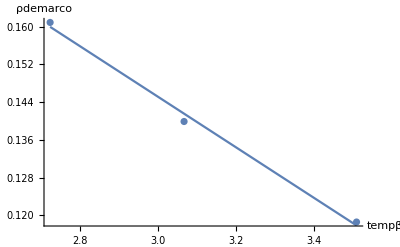

0.0256142-0.00562732 x

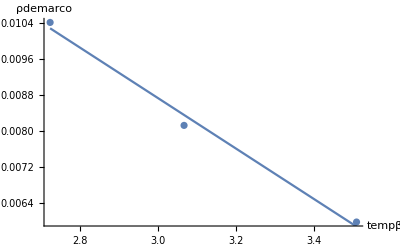

```mathematica
(*calculate tempβ related err slope*)
iitempβlength=3;
tempβrelatederrslopelist={0};
For[iitempβ=1,iitempβ≤ iitempβlength,iitempβ++,
{
(*find corresponding μ and temp list*)
μchecktemp=μfit;
tempβcheck=tempβerrlisttemp⟦iitempβ⟧;
(*find corresponding μ and temp list*)
(*data interpolation*)
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,3}⟧]];
densityerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,4}⟧]];
doubloncheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,5}⟧]];
doublonerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,6}⟧]];
finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=Quiet[ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx];
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0]  ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0]  ]^2)^0.5]; 
(*data interpolation*)

(*calculated demarco density err*)
iixmax=40;
iiymax=40;
iizmax=20;
finalρfunc3d[iix_,iiy_,iiz_]:=Quiet[densitycheckfunc[μchecktemp-vext[iix,iiy,iiz]]];
final3dρlist=Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];
final3ddoublonlist=Table[{iix,iiy,iiz,Max[0,finaldoublon3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];
dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4 ⟧^2,{ii,1,Length[ls3dρ]}]];
ntot=Total[ls3dρ⟦All,4⟧];
ρdemarco=ρdemarcon2/ntot;
doublondemarcon2=Total[Table[ls3dρ⟦ii,4⟧*ls3ddoublon⟦ii,4⟧,{ii,1,Length[ls3dρ]}]];
doublondemarco=doublondemarcon2/ntot;
tempβrelatederrslopelisttemp={{tempβcheck,ρdemarco,doublondemarco}};
Print[tempβrelatederrslopelisttemp];
tempβrelatederrslopelist=Join[tempβrelatederrslopelist,tempβrelatederrslopelisttemp]; 
(*calculated demarco density err*)
}
]
tempβrelatederrslopelistfinal=tempβrelatederrslopelist⟦2;;iitempβlength+1,{1,2}⟧;
soltempβ=Fit[tempβrelatederrslopelistfinal,{1,x},x]
Show[ListPlot[tempβrelatederrslopelistfinal,AxesLabel->{"tempβ","ρdemarco"}],Plot[soltempβ,{x,Min[tempβerrlisttemp⟦1;;3⟧],Max[tempβerrlisttemp⟦1;;3⟧]}]]
tempβrelatedslope=soltempβ⟦2,1⟧;

tempβrelateddoublonerrslopelistfinal=tempβrelatederrslopelist⟦2;;iitempβlength+1,{1,3}⟧;
soltempβdoublon=Fit[tempβrelateddoublonerrslopelistfinal,{1,x},x]
Show[ListPlot[tempβrelateddoublonerrslopelistfinal,AxesLabel->{"tempβ","ρdemarco"}],Plot[soltempβdoublon,{x,Min[tempβerrlisttemp⟦1;;3⟧],Max[tempβerrlisttemp⟦1;;3⟧]}]]
tempβrelateddoublonslope=soltempβdoublon⟦2,1⟧;
```

```mathematica
f0horizontal=f0;
f0vertical=√(fz^2+(xdtfreq*200/30)^2);
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;
dx=1;
dy=1;
dz=1;
tempβcheck=tempβfit;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,3}⟧]];
densityerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,4}⟧]];
doubloncheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,5}⟧]];
doublonerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,6}⟧]];

finalρfunc3d[iix_,iiy_,iiz_]:=densitycheckfunc[μfit-vext[iix,iiy,iiz]];
finalρerrfunc3d[iix_,iiy_,iiz_]:=densityerrcheckfunc[μfit-vext[iix,iiy,iiz]];
doublonρfunc3d[iix_,iiy_,iiz_]:=doubloncheckfunc[μfit-vext[iix,iiy,iiz]];
doublonρerrfunc3d[iix_,iiy_,iiz_]:=doublonerrcheckfunc[μfit-vext[iix,iiy,iiz]];

iixmax=40;
iiymax=40;
iizmax=20;
final3dρlist=Quiet[Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];
final3dρerrlist=Quiet[Table[{iix,iiy,iiz,Max[0,Abs[finalρerrfunc3d[iix,iiy,iiz]]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];
final3ddoublonlist=Quiet[Table[{iix,iiy,iiz,Max[0,doublonρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];
final3ddoublonerrlist=Quiet[Table[{iix,iiy,iiz,Max[0,doublonρerrfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];

dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3dρerr=ArrayReshape[final3dρerrlist,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];
ls3ddoublonerr=ArrayReshape[final3ddoublonerrlist,{dimlsleng,4}];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4⟧^2,{ii,1,Length[ls3dρ]}]];
nsquaretot=ρdemarcon2;
ntot=Total[ls3dρ⟦All,4⟧];
dbtot=Total[ls3ddoublon⟦All,4⟧*ls3dρ⟦All,4⟧];

lsρdemarcoerr= Table[(((2*ls3dρ⟦ii,4⟧)/ntot+nsquaretot/ntot^2)ls3dρerr⟦ii,4⟧)^2,{ii,1,Length[ls3dρ]}];
lsdoublongdemarcoerr1=Table[
(
((ls3ddoublonerr⟦ii,4⟧*ls3dρ⟦ii,4⟧)/ntot)^2+((ls3ddoublon⟦ii,4⟧*ls3dρerr⟦ii,4⟧)/ntot)^2+((ls3ddoublon⟦ii,4⟧*ls3dρ⟦ii,4⟧)/ntot^2)^2
),{ii,1,Length[ls3dρ]}];

dbcenterfraction=doublonρfunc3d[0,0,0]/finalρfunc3d[0,0,0];
dbfraction=Total[ls3ddoublon⟦All,4⟧]/ntot;


Print[StringJoin["center doublon fraction:   ", ToString[dbcenterfraction]]];
Print[StringJoin["total doublon fraction:   ", ToString[dbfraction]]];

ntot=Total[ls3dρ⟦All,4⟧];

ρdemarco=nsquaretot/ntot;
dbdemarco=dbtot/ntot;
ρdemarcoerr=Sqrt[Total[lsρdemarcoerr]+(tempβrelatedslope *√(tempβfiterr^2+(0.04 tempβfit^2)^2))^2+(μrelatedslope*μfiterr)^2];
dbdemarcoerr=Sqrt[Total[lsdoublongdemarcoerr1]+(tempβrelateddoublonslope *(tempβfiterr+0.04 tempβfit^2))^2+(μrelateddoublonslope*μfiterr)^2];
Print[StringJoin["density weighted doublon:",ToString[dbdemarco]]];
Print["density weighted doublon errbar:"]
dbdemarcoerr
Print[StringJoin["density weighted density:   ", ToString[ρdemarco]]];
Print["density weighted density errbar:"];
ρdemarcoerr
```

center doublon fraction:   0.0977845

total doublon fraction:   0.041285

density weighted doublon:0.00812055

density weighted doublon errbar:

0.00462145

density weighted density:   0.139879

density weighted density errbar:

0.0313589

## Calculate 3-D density

```mathematica
f0horizontal=f0;
f0vertical=√(fz^2+(xdtfreq*200/30)^2);
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;
dx=1;
dy=1;
dz=1;
finalρfunc3d[iix_,iiy_,iiz_]:=densitycheckfunc[μfit-vext[iix,iiy,iiz]];
finalρerrfunc3d[iix_,iiy_,iiz_]:=densityerrcheckfunc[μfit-vext[iix,iiy,iiz]];
doublonρfunc3d[iix_,iiy_,iiz_]:=doubloncheckfunc[μfit-vext[iix,iiy,iiz]];

final3dρlist=Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];
final3dρerrlist1=Table[{iix,iiy,iiz,(2Max[0,finalρfunc3d[iix,iiy,iiz]]*Max[0,Abs[finalρerrfunc3d[iix,iiy,iiz]]])^2},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];
final3dρerrlist2=Table[{iix,iiy,iiz,(Max[0,Abs[finalρerrfunc3d[iix,iiy,iiz]]])^2},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];
final3ddoublonlist=Table[{iix,iiy,iiz,Max[0,doublonρfunc3d[iix,iiy,iiz]]},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];


dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3dρerr1=ArrayReshape[final3dρerrlist1,{dimlsleng,4}];
ls3dρerr2=ArrayReshape[final3dρerrlist2,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];


dbcenterfraction=doublonρfunc3d[0,0,0]/finalρfunc3d[0,0,0];
dbfraction=Total[ls3ddoublon⟦All,4⟧]/Total[ls3dρ⟦All,4⟧];
Print[StringJoin["center doublon fraction:   ", ToString[dbcenterfraction]]];
Print[StringJoin["total doublon fraction:   ", ToString[dbfraction]]];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4⟧^2,{ii,1,Length[ls3dρ]}]];
ntot=Total[ls3dρ⟦All,4⟧];

ρdemarco=ρdemarcon2/ntot;
ρdemarcoerr=Sqrt[Total[ls3dρerr1⟦All,4⟧]/ρdemarcon2^2+Total[ls3dρerr2⟦All,4⟧]/ntot^2]ρdemarco;
Print[StringJoin["density weighted density:   ", ToString[ρdemarco]]];
Print["density weighted density errbar:"];
ρdemarcoerr*10^5
```

InterpolatingFunction::dmval: Input value {-7.12093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.51632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.92387} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-7.12093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.51632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-7.12093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.51632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.92387} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-7.12093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.51632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.92387} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

center doublon fraction:   0.0672457

total doublon fraction:   0.0262328

density weighted density:   0.089585

density weighted density errbar:

3.42031

```mathematica
Export["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\Monte Carlo\\quest-1.4.4\\test1\\2.5Er 206G\\2.5Er 206G density.txt", ls3dρ, "TSV"]
Export["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\Monte Carlo\\quest-1.4.4\\test1\\2.5Er 206G\\2.5Er 206G density error.txt", ls3dρerr, "TSV"]
Export["H:\\UofT Ultracold Atoms Lab\\Projects\\Conductivity\\Monte Carlo\\quest-1.4.4\\test1\\2.5Er 206G\\2.5Er 206G doublon.txt", ls3ddoublon, "TSV"]
```

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\Monte Carlo\quest-1.4.4\test1\2.5Er 206G\2.5Er 206G density.txt

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\Monte Carlo\quest-1.4.4\test1\2.5Er 206G\2.5Er 206G density error.txt

H:\UofT Ultracold Atoms Lab\Projects\Conductivity\Monte Carlo\quest-1.4.4\test1\2.5Er 206G\2.5Er 206G doublon.txt